```mathematica
f[i_,a_,slope0_,curve0_]:= Block[{x,y,b,c},
x = Exp[slope0];
y = (-Exp[curve0+slope0]);
c = x/y*(a-1);
b = x/a*c^(1-a);
Return[b*((i+c)^a - c^a)]]
dfdi[i_,a_,slope0_,curve0_]:= Block[{x,y,b,c},
x = Exp[slope0];
y = (-Exp[curve0+slope0]);
c = x/y*(a-1);
b = x/a*c^(1-a);
Return[a*b*(i+c)^(a-1)]]
```

```mathematica
Manipulate[Plot[f[i,a,slope0,curve0],{i,0,1},PlotRange->{{0,1},{0,0.03}}],{a,-100.0,0.0},{slope0,-2,2},{curve0,1,5}]
```

```mathematica
Manipulate[Plot[dfdi[i,a,slope0,curve0],{i,0,1},PlotRange->{{0,1},{0,0.2}}],{a,-100.0,0.0},{slope0,-2,2},{curve0,1,5}]
```

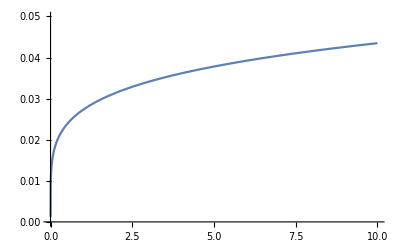

```mathematica
g[i_]:= Exp[-3.6]*i^(Exp[-1.6]);
Plot[g[i],{i,0,10},PlotRange->{Automatic,{0,0.05}}]
```